```mathematica
W[zm_,ym_,b_,h_?NumericQ] := NIntegrate[(Sqrt[(zm - b/2 Cos[t])^2 + (ym - h  Sin[t])^2])^(1/7) * Cos[ArcTan[Abs[((b*Tan[t])/(2*h)-(ym - h Sin[t])/(zm - b/2 * Cos[t]))/ (1 + (b*Tan[t])/(2*h) *(ym - h Sin[t]) / (zm - b/2 * Cos[t]))]]],{t,Pi,2Pi}] /; zm^2/(b/2)^2 + ym^2/h^2 - 1 <0 ;
W[zm_,ym_,b_,h_?NumericQ] := 0 /; zm^2/(b/2)^2 + ym^2/h^2 - 1≥0
```

Gennaio

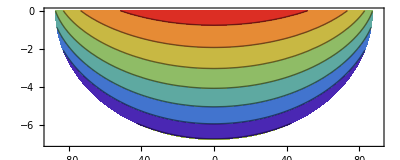

```mathematica
Gennaio
ContourPlot[0.7320201538672618 W[zm,ym,180,7],{zm,-90,90},{ym,0,-7},RegionFunction->Function[{x,y},(x)^2/90^2+y^2/7^2 - 1 < - 0.06],Contours->{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1,1.1,1.2,1.3,1.4}, ContourShading->Automatic,ColorFunction->"Rainbow",PlotLegends->Automatic,AspectRatio->2/5]
```

Febbraio

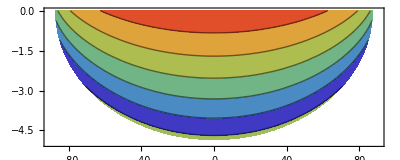

```mathematica
Febbraio
ContourPlot[0.8849158632608528 W[zm,ym,180,5],{zm,-90,90},{ym,0,-5},RegionFunction->Function[{x,y},(x)^2/90^2+y^2/5^2 - 1 < - 0.06],Contours->{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1,1.1,1.2,1.3,1.4}, ContourShading->Automatic,ColorFunction->"Rainbow",PlotLegends->Automatic,AspectRatio->2/5]
```

Marzo

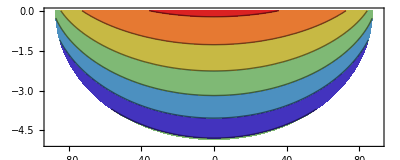

```mathematica
Marzo
ContourPlot[0.7584993113664453 W[zm,ym,180,5],{zm,-90,90},{ym,0,-5},RegionFunction->Function[{x,y},(x)^2/90^2+y^2/5^2 - 1 < - 0.06],Contours->{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1,1.1,1.2,1.3,1.4}, ContourShading->Automatic,ColorFunction->"Rainbow",PlotLegends->Automatic,AspectRatio->2/5]
```

```mathematica
ContourPlot[0.7584993113664453 W[zm,ym,180,5],{zm,-90,90},{ym,0,-5},RegionFunction->Function[{x,y},(x)^2/90^2+y^2/5^2 - 1 < - 0.06],Contours->{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1,1.1,1.2,1.3,1.4}, ContourShading->Automatic,ColorFunction->[Hue[0.7584993113664453 W[zm,ym,180,5]]],PlotLegends->Automatic,AspectRatio->2/5]
```

```mathematica
Maggio
```

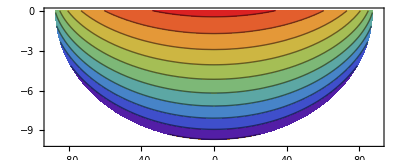

```mathematica
ContourPlot[0.7826734508367231 W[zm,ym,180,10],{zm,-90,90},{ym,0,-10},RegionFunction->Function[{x,y},(x)^2/90^2+y^2/10^2 - 1 < - 0.06],Contours->{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.0,2.1}, ContourShading->Automatic,ColorFunction->"Rainbow",PlotLegends->Automatic,AspectRatio->2/5]
```

Giugno

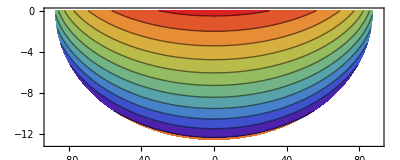

```mathematica
Giugno
ContourPlot[0.7315255756035324 W[zm,ym,180,13],{zm,-90,90},{ym,0,-13},RegionFunction->Function[{x,y},(x)^2/90^2+y^2/13^2 - 1 < - 0.06],Contours->{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.0,2.1,2.2,2.3}, ContourShading->Automatic,ColorFunction->"Rainbow",PlotLegends->Automatic,AspectRatio->2/5]
```

Luglio

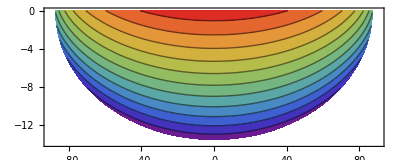

```mathematica
Luglio
ContourPlot[0.7458646098410179 W[zm,ym,180,14],{zm,-90,90},{ym,0,-14},RegionFunction->Function[{x,y},(x)^2/90^2+y^2/14^2 - 1 < - 0.06],Contours->{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.0,2.1,2.2,2.3}, ContourShading->Automatic,ColorFunction->"Rainbow",PlotLegends->Automatic,AspectRatio->2/5]
```

Agosto

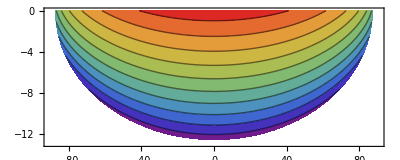

```mathematica
Agosto
ContourPlot[0.7044320357663646 W[zm,ym,180,13],{zm,-90,90},{ym,0,-13},RegionFunction->Function[{x,y},(x)^2/90^2+y^2/13^2 - 1 < - 0.06],Contours->{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.0,2.1,2.2,2.3}, ContourShading->Automatic,ColorFunction->"Rainbow",PlotLegends->Automatic,AspectRatio->2/5]
```

Settembre

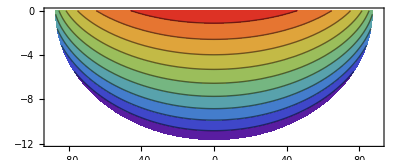

```mathematica
Settembre
ContourPlot[0.707340977940588 W[zm,ym,180,12],{zm,-90,90},{ym,0,-12},RegionFunction->Function[{x,y},(x)^2/90^2+y^2/12^2 - 1 < - 0.06],Contours->{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.0,2.1,2.2,2.3}, ContourShading->Automatic,ColorFunction->"Rainbow",PlotLegends->Automatic,AspectRatio->2/5]
```

Ottobre

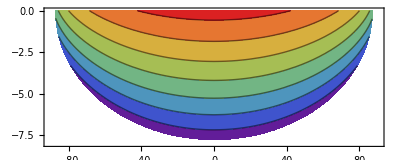

```mathematica
Ottobre
ContourPlot[0.7076019085139525 W[zm,ym,180,8],{zm,-90,90},{ym,0,-8},RegionFunction->Function[{x,y},(x)^2/90^2+y^2/8^2 - 1 < - 0.06],Contours->{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.0,2.1,2.2,2.3}, ContourShading->Automatic,ColorFunction->"Rainbow",PlotLegends->Automatic,AspectRatio->2/5]
```

Novembre

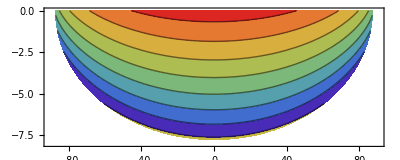

```mathematica
Novembre
ContourPlot[0.7665687342234486 W[zm,ym,180,8],{zm,-90,90},{ym,0,-8},RegionFunction->Function[{x,y},(x)^2/90^2+y^2/8^2 - 1 < - 0.06],Contours->{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.0,2.1,2.2,2.3}, ContourShading->Automatic,ColorFunction->"Rainbow",PlotLegends->Automatic,AspectRatio->2/5]
```